# Eisenstein & Hu, 1998

An implementation of portions of the code from Eisenstein & Hu, ApJ 1998.

```mathematica
(* Formulae in Eisenstein & Hu ApJ, 1998 *)

BeginPackage["Cosmology`EH98`"];

zeqEH::usage = "zeqEH[cosmo] returns the equality redshift (Eq. 2, EH98)";
keqEH::usage = "keqEH[cosmo] returns k_eq in Mpc^-1 (Eq. 3, EH98)";
zdecEH::usage = "zdecEH[cosmo] returns the decoupling redshift (Eq. 4, EH98)";
rsEH::usage = "rsEH[cosmo] returns the sound horizon in Mpc(Eq.6, EH98)";
tkEH::usage = "tkEH[k, cosmo] returns the transfer fn at k (in h^-1 Mpc)";
pkEH::usage = "pkEH[k, ns, deltah2, cosmo] returns the no-wiggle power spectrum at k.";

Needs["Cosmology`Defs`"];
```

```mathematica
Begin["`Private`"];
```

## Sound horizons, matter-radiation equality etc.

```mathematica
(* Eq. 2 *) 
zeqEH[cosmo_?OptionQ] := Module[{om,t0},
            om = OmegaMh2 /. cosmo;
            t0 = (TCMB/2.7) /. cosmo;
            2.5 * 10.0^4 * om * t0^-4
            ]; 

(* Eq 3 *)

keqEH[cosmo_?OptionQ] := Module[{om, t0},
            om = OmegaMh2 /. cosmo;
            t0 = (TCMB/2.7) /. cosmo;
            7.46 * 10^-2 * om * t0^-2
            ];

(* Eq 4 *) 

zdecEH[cosmo_?OptionQ] := Module[{om,ob,b1, b2}, 
    om = OmegaMh2 /. cosmo;
    ob = Omegabh2 /. cosmo;
    b2 = 0.238*om^0.223;
    b1 = 0.313*om^-0.419 * (1.0 + 0.607 * om^0.674);
    1291 * om^0.251 * (1.0+b1*ob^b2)/(1.0 + 0.659*om^0.828)
    ];


Rsound[z_, cosmo_?OptionQ] := Module[{ob, t0}, 
    t0 = (TCMB/2.7) /. cosmo;
    ob = Omegabh2 /. cosmo;
    31.5*ob*t0^-4 / (z/1000.0)
    ];

rsEH[cosmo_?OptionQ] := Module[{keq, zeq, zd, req, rd}, 
  keq = keqEH[cosmo];
  zeq = zeqEH[cosmo]; zd = zdecEH[cosmo];
  req = Rsound[zeq, cosmo]; rd = Rsound[zd, cosmo];
  (2./3/keq) * Sqrt[6./req] * Log[ (Sqrt[1.0+ rd] + Sqrt[rd + req])/(1.0+Sqrt[req])]
  ];
```

## No-wiggle transfer function

```mathematica
tkEH[k_, cosmo_?OptionQ] := Module[{ag, rs, geff, ob, om, q, t0, l0, c0, g0}, 
	rs = rsEH[cosmo];
    ob = Omegabh2 /. cosmo;
    om = OmegaMh2 /. cosmo;
    ag = 1.0 - 0.328*Log[431*om] * (ob/om) + 0.38 * Log[22.3*om]*(ob/om)^2;
    g0 = om/Hubble[1.0, cosmo];
    geff = g0 * (ag + (1.0-ag)/(1.0 + (0.43*k*rs)^4));
    t0 = (TCMB/2.7) /. cosmo;
    q = k * t0^2 / geff;
    c0 = 14.2 + 731.0/(1+62.5*q);
    l0 = Log[2*Exp[1.0] + 1.8*q];
    l0/(l0 + c0*q^2)
    ];
```

## No-wiggle P(k)

Since I perpetually get confused by the normalization of this, I will be explicit here. This is following Bunn & White, ApJ 1997.
	\Delta^2(k) = k^3 P(k)/ 2 \pi^2 = deltah^2 * (k/H0/c)^(3+ns) T^2(k)
A reasonable starting guess for deltah2 ~ 10^-10

```mathematica
pkEH[k_, ns_, deltah2_, cosmo_?OptionQ] := Module[{k1, t1, Hbyc},
	Hbyc = 100.0/299792.458; 
	t1 = tkEH[k, cosmo];
	deltah2*(k/Hbyc)^ns * (1/Hbyc)^3 * t1^2 * 2*Pi^2 
];
```

```mathematica
End[];
EndPackage[];
```

## Examples

```mathematica
Needs["Cosmology`Defs`"]
```

```mathematica
FoMSWG
```

{Omegabh2→0.0227,OmegaMh2→0.1326,OmegaKh2→0.,OmegaDEh2→0.3844,ns→0.963,w0→-1.,wa→0.,TCMB→2.726,gamma→0.55}

#### Test the sound horizon

```mathematica
rs =rsEH[FoMSWG]
```

153.567

#### Get the hubble constant

```mathematica
h = Hubble[1.0, FoMSWG]
```

0.719027

#### Test vectorized nature of T(k)

```mathematica
tkEH[{0.001, 1.0}, FoMSWG]
```

{0.990051,0.00366988}

#### Test vectorized nature of P(k)

```mathematica
pkEH[{0.001, 1.0}, 1.0, 10^-10,FoMSWG]
```

{156.289,2.14741}

#### Plot T(k)

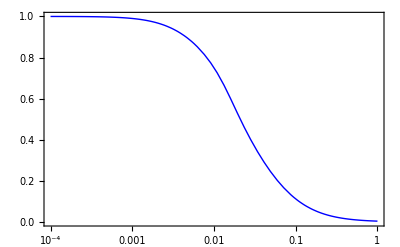

```mathematica
LogLinearPlot[tkEH[k,FoMSWG], {k, 10^-4, 1}, 
                             {Frame-> True, Axes-> False, 
                            PlotStyle-> {Thick, Blue}}]
```

#### Plot P(k)

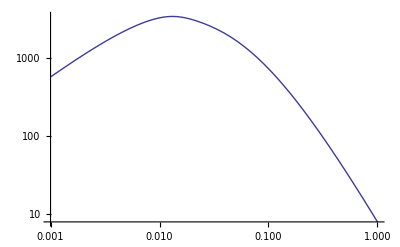

```mathematica
LogLogPlot[pkEH[k,1.0, 3.68 10^-10, FoMSWG], {k, 10^-3, 1}]
```